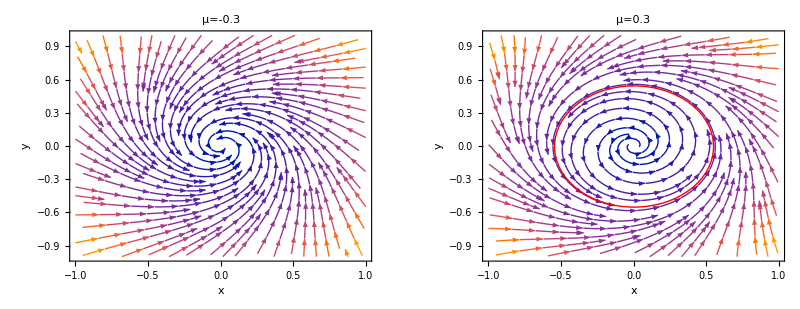

```mathematica
GraphicsRow[{With[{μ=-0.3},StreamPlot[{μ x-y-x(x^2+y^2),x+μ y-y(x^2+y^2)},{x,-1,1},{y,-1,1},AspectRatio->0.8,PlotLabel->"μ=-0.3",FrameLabel->{"x","y"}]],With[{μ=0.3},StreamPlot[{μ x-y-x(x^2+y^2),x+μ y-y(x^2+y^2)},{x,-1,1},{y,-1,1},Epilog->{Red,Circle[{0,0},√0.3]},AspectRatio->0.8,PlotLabel->"μ=0.3",FrameLabel->{"x","y"}]]}]
```

```mathematica
Series[(α r+ξ r^3+r^5 g1[ϕ])/(ω+η r^2+r^4 g2[ϕ]),{r,0,3}]
```

(α r)/ω+((-α η+ξ ω) r^3)/ω^2+O[r]^4

```mathematica
DSolve[{r'[ϕ]==(α r[ϕ])/ω,r[0]==r0},r[ϕ],ϕ]
```

{{r[ϕ]→ⅇ^((α ϕ)/ω) r0}}

```mathematica
DSolve[{u'[ϕ]==(α u[ϕ])/ω+(ⅇ^((α ϕ)/ω))^3(-α η+ξ ω)/ω^2,u[0]==0},u[ϕ],ϕ]//Simplify
```

{{u[ϕ]→-(ⅇ^((α ϕ)/ω) (-1+ⅇ^((2 α ϕ)/ω)) (α η-ξ ω))/(2 α ω)}}

```mathematica
Limit[-(ⅇ^((α ϕ)/ω) (-1+ⅇ^((2 α ϕ)/ω)) (α η-ξ ω))/(2 α ω),α->0]
```

(ξ ϕ)/ω

```mathematica
-(ⅇ^((α ϕ)/ω) (-1+ⅇ^((2 α ϕ)/ω)) (α η-ξ ω))/(2 α ω)//Simplify
```

-(ⅇ^((α ϕ)/ω) (-1+ⅇ^((2 α ϕ)/ω)) (α η-ξ ω))/(2 α ω)

```mathematica
ClearAll["Global`*"];
(*f:向量场或映射 (List) x:自变量列表 (List) a:展开点 (List) k:多重线性型的阶数 (Integer)*)
MultilinearForm[f_,x_,a_,k_]:=Module[{tensorD},tensorD=D[f,{x,k}]/. Thread[x->a];
Function[Null,Block[{vecs={##}},Fold[Dot,tensorD,Reverse[vecs]]]]];
vars={x,y};
f={y,(α-x^2)y-x};
B=MultilinearForm[f,{x,y},{0,0},2];
CC=MultilinearForm[f,{x,y},{0,0},3];
B[Table[Subscript[ξ, i],{i,1,2}],Table[Subscript[η, i],{i,1,2}]]
CC[Table[Subscript[ξ, i],{i,1,2}],Table[Subscript[η, i],{i,1,2}],Table[Subscript[γ, i],{i,1,2}]]
Grad[f,{x,y}]/.{x->0,y->0}
Grad[f,{x,y}]/.{x->0,y->0}//Eigenvalues
Grad[f,{x,y}]/.{x->0,y->0}//Eigensystem
Transpose[Grad[f,{x,y}]]/.{x->0,y->0}//Eigensystem
```

{0,0}

{0,(-2 γ_2 η_1-2 γ_1 η_2) ξ_1-2 γ_1 η_1 ξ_2}

{{0,1},{-1,α}}

{1/2 (α-√(-4+α^2)),1/2 (α+√(-4+α^2))}

{{1/2 (α-√(-4+α^2)),1/2 (α+√(-4+α^2))},{{1/2 (α+√(-4+α^2)),1},{1/2 (α-√(-4+α^2)),1}}}

{{1/2 (α-√(-4+α^2)),1/2 (α+√(-4+α^2))},{{1/2 (-α-√(-4+α^2)),1},{1/2 (-α+√(-4+α^2)),1}}}

```mathematica
MyDot[x_,y_]:=Dot[Conjugate[x],y]
MySimplify[x_]:=Simplify[x,Assumptions->α∈Reals&&√(4-α^2)>0]
q={1/2 (α-I √(4-α^2)),1};
p={1/2 (-α-I √(4-α^2)),1}/(MyDot[q,{1/2 (-α-I √(4-α^2)),1}]//Expand//MySimplify);
MyDot[q,p]//Expand//MySimplify
```

1

```mathematica
ω=√(4-α^2);
g20=MyDot[p,B[q,q]]//MySimplify;
g11=MyDot[p,B[q,Conjugate[q]]]//MySimplify;
g21=MyDot[p,CC[q,q,Conjugate[q]]]//MySimplify;
1/(2 ω^2)Re[I g20 g11+ω g21]//MySimplify
```

-Re[(√(4-α^2) (2+α^2-ⅈ α √(4-α^2)))/(-4+α^2-ⅈ α √(4-α^2))]/(-4+α^2)

```mathematica
√(4-α^2) (2+α^2-ⅈ α √(4-α^2))(-4+α^2+ⅈ α √(4-α^2))//MySimplify
(-4+α^2-ⅈ α √(4-α^2))(-4+α^2+ⅈ α √(4-α^2))//MySimplify
```

2 (-4+α^2) (-3 ⅈ α+√(4-α^2))

-4 (-4+α^2)

```mathematica
(-4+α^2-ⅈ α √(4-α^2))(-4+α^2+ⅈ α √(4-α^2))//Expand
```

16-4 α^2

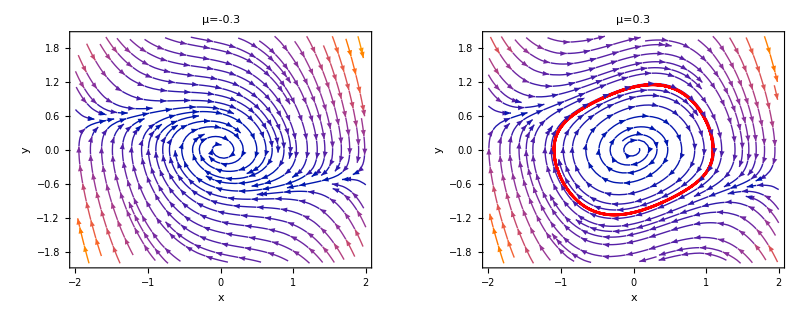

```mathematica
sol=NDSolve[{x'[t]==y[t],y'[t]==(0.3-x[t]^2)y[t]-x[t],x[0]==√0.3,y[0]==0},{x,y},{t,0,100}];

GraphicsRow[{With[{μ=-0.3},StreamPlot[{y,(μ-x^2)y-x},{x,-2,2},{y,-2,2},AspectRatio->0.8,PlotLabel->"μ=-0.3",FrameLabel->{"x","y"}]],With[{μ=0.3},Show[StreamPlot[{y,(μ-x^2)y-x},{x,-2,2},{y,-2,2},AspectRatio->0.8,PlotLabel->"μ=0.3",FrameLabel->{"x","y"}],ParametricPlot[{x[t],y[t]}/.sol,{t,80,100},PlotStyle->{Thickness[0.005],Red}]]]}]
```

```mathematica
ClearAll["Global`*"];
(*f:向量场或映射 (List) x:自变量列表 (List) a:展开点 (List) k:多重线性型的阶数 (Integer)*)
MultilinearForm[f_,x_,a_,k_]:=Module[{tensorD},tensorD=D[f,{x,k}]/. Thread[x->a];
Function[Null,Block[{vecs={##}},Fold[Dot,tensorD,Reverse[vecs]]]]];
vars={x,y};
f={a-(μ+1)x+x^2 y,μ x-x^2 y};
B=MultilinearForm[f,{x,y},{0,0},2];
CC=MultilinearForm[f,{x,y},{0,0},3];
CC[Table[Subscript[ξ, i],{i,1,2}],Table[Subscript[η, i],{i,1,2}],Table[Subscript[γ, i],{i,1,2}]]
MyDot[x_,y_]:=Dot[Conjugate[x],y]
MySimplify[x_]:=Simplify[x,Assumptions->a∈Reals&&a>0]
Eigensystem[{{-(1+μ),a^2},{μ,-a^2}}]
Eigensystem[Transpose[{{-(1+μ),a^2},{μ,-a^2}}]]
```

{(2 γ_2 η_1+2 γ_1 η_2) ξ_1+2 γ_1 η_1 ξ_2,(-2 γ_2 η_1-2 γ_1 η_2) ξ_1-2 γ_1 η_1 ξ_2}

{{1/2 (-1-a^2-μ-√(-4 a^2+(1+a^2+μ)^2)),1/2 (-1-a^2-μ+√(-4 a^2+(1+a^2+μ)^2))},{{-(1-a^2+μ+√(1-2 a^2+a^4+2 μ+2 a^2 μ+μ^2))/(2 μ),1},{-(1-a^2+μ-√(1-2 a^2+a^4+2 μ+2 a^2 μ+μ^2))/(2 μ),1}}}

{{1/2 (-1-a^2-μ-√(-4 a^2+(1+a^2+μ)^2)),1/2 (-1-a^2-μ+√(-4 a^2+(1+a^2+μ)^2))},{{-(1-a^2+μ+√(1-2 a^2+a^4+2 μ+2 a^2 μ+μ^2))/(2 a^2),1},{-(1-a^2+μ-√(1-2 a^2+a^4+2 μ+2 a^2 μ+μ^2))/(2 a^2),1}}}

```mathematica
q={-(1-a^2+μ-I √(4 a^2-(1+a^2+μ)^2))/(2 μ),1};
p={-(1-a^2+μ+I √(4 a^2-(1+a^2+μ)^2))/(2 a^2),1}/(MyDot[q,{-(1-a^2+μ+I √(4 a^2-(1+a^2+μ)^2))/(2 a^2),1}]//Expand//MySimplify);
MyDot[q,p]//Expand//MySimplify
MyDot[Conjugate[q],p]//Expand//MySimplify
```

1

0

```mathematica
ω=√(4 a^2-(1+a^2+μ)^2);
g20=MyDot[p,B[q,q]]/.{μ->-(1+a^2)}//MySimplify//MySimplify
g11=MyDot[p,B[q,Conjugate[q]]]/.{μ->-(1+a^2)}//MySimplify//MySimplify
g21=MyDot[p,CC[q,q,Conjugate[q]]]/.{μ->-(1+a^2)}//MySimplify//MySimplify
1/(2ω)Re[I g20 g11+ω g21]/.{μ->-(1+a^2)}//MySimplify
```

0

0

-(a (-ⅈ+3 a))/(1+a^2)

-(3 a^2)/(2+2 a^2)